```mathematica
p=0.99
```

0.99

```mathematica
Clear[arg,log];
arg[z_,σ_:-Pi]:=Arg[z Exp[-I (σ+Pi)]]+σ+Pi;
log[z_,σ_:-Pi]:=Log[Abs[z]]+I arg[z,σ]
g[z_,p_]:=E^((p-1)log[z,0])/(z+1) 
f[z_]:=g[z,p]
Cont1[t_,eps_]:= t+I eps
Cont2[t_,r_,th_]:=r(Cos[t+th]+ I Sin[t+th])
```

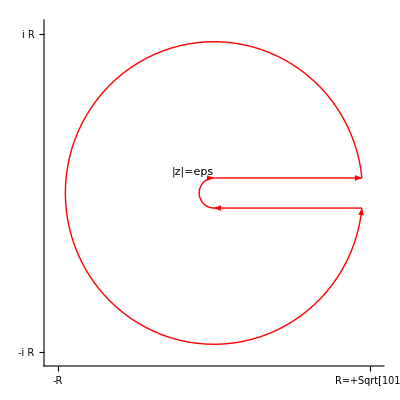

```mathematica
lin[x_]:={Arrowheads[{{0.05,0.5}}],Arrow[Most@x]};
arc[x_]:={Arrowheads[{{0.05,0.5}}],Arrow[Table[x[[1]] {Cos[j],x[[4]] Sin[j]},{j,x[[2]],x[[3]],0.01 (x[[3]]-x[[2]])}]]};
cont[lst_]:=If[#[[-1]]=="line",lin@#,arc@#]&/@lst

im1[eps_,l_]:=Graphics[{Red,cont[{{{0,eps},{l,eps},"line"},{Norm[{l,eps}],ArcTan[eps/l],2 Pi-ArcTan[eps/l],1,"arc"},{{l,-eps},{0,-eps},"line"},{eps,Pi/2,3 Pi/2,-1,"arc"}}],Black,Text["|z|=eps",2 eps {Cos[3 Pi/4],Sin[3 Pi/4]}]},Axes->True,Ticks->{{{Norm[{l,eps}]+0.5,"R="+ToString[Norm[{l,eps}]]},{-Norm[{l,eps}]-0.5,"-R"}},{{Norm[{l,eps}]+0.5,"i R"},{-Norm[{l,eps}]-0.5,"-i R"}}},PlotRange->{{-Norm[{l,eps}]-1,Norm[{l,eps}]+1},{-Norm[{l,eps}]-1,Norm[{l,eps}]+1}}]
im1[1,10]
```

```mathematica
SommaDiRiemannL[range_,epsi_,n_]:=
(deltat=range/2^n;
If[range>0,t=0,t=-range+deltat];
zb=Cont1[t,epsi];
Somma=0;  For[k=0,k<2^n,k++,za=zb;
t+=deltat;
zb=Cont1[t,epsi];
Somma+= f[za]*(zb-za)];
Return[N[Somma]])
SommaDiRiemannC[range_,raggio_,fase_,n_]:= 
( deltat=range/2^n;
t=0;
zb=Cont2[t,raggio,fase];
Somma=0;  For[k=0,k<2^n,k++,za=zb;
t+=deltat;
zb=Cont2[t,raggio,fase];
Somma+= f[za]*(zb-za)];
Return[N[Somma]])
```

```mathematica
l=1000;epsi=0.1;n=16;
r=Sqrt[l^2+epsi^2];pha=ArcTan[epsi/l];

a=SommaDiRiemannL[l,epsi,n];
ar=NIntegrate[Re[f[Cont1[t,epsi]]],{t,0,l},AccuracyGoal->10];
ai=NIntegrate[Im[f[Cont1[t,epsi]]],{t,0,l},AccuracyGoal->10];
b=SommaDiRiemannC[2 Pi-2pha,r,pha,n];
br=NIntegrate[Re[f[Cont2[t,r,pha]]*D[Cont2[t,r,pha],t]],{t,0,2 Pi-2pha},AccuracyGoal->10];
bi=NIntegrate[Im[f[Cont2[t,r,pha]]*D[Cont2[t,r,pha],t]],{t,0,2 Pi-2pha},AccuracyGoal->10];
c=SommaDiRiemannL[-l,-epsi,n];
cr=NIntegrate[Re[f[Cont1[t,-epsi]]],{t,l,0},AccuracyGoal->10];
ci=NIntegrate[Im[f[Cont1[t,-epsi]]],{t,l,0},AccuracyGoal->10];
d=SommaDiRiemannC[-Pi,epsi,3Pi/2,n];
dr=NIntegrate[Re[f[Cont2[t,epsi,Pi/2]]*D[Cont2[t,epsi,Pi/2],t]],{t,Pi,0},AccuracyGoal->10];
di=NIntegrate[Im[f[Cont2[t,epsi,Pi/2]]*D[Cont2[t,epsi,Pi/2],t]],{t,Pi,0},AccuracyGoal->10];
Print["\nValori teorici:"]
If[ai>0,Print["a=",ar"+",ai," i"],Print["a=",ar,ai," i"]];
If[bi>0,Print["b=",br"+",bi," i"],Print["b=",br,bi," i"]];
If[ci>0,Print["c=",cr"+",ci," i"],Print["c=",cr,ci," i"]];
If[di>0,Print["d=",dr"+",di," i"],Print["d=",dr,di," i"]];
If[ai+bi+ci+di>0,Print["Somma=",ar+br+cr+dr,"+",ai+bi+ci+di," i"],Print["Somma=",ar+br+cr+dr,ai+bi+ci+di," i"]];
Print["\nValori approssimati da somma di Riemann:"]
Print["a=",a]
Print["b=",b]
Print["c=",c]
Print["d=",d]
Print["a+b+c+d=",a+b+c+d]
```

Valori teorici:

a=6.68521-0.102836 i

b=0.184149 +5.85971 i

c=-6.67848 +0.317134 i

d=0.00647629 +0.206079 i

Somma=0.19736+6.28008 i

Valori approssimati da somma di Riemann:

a=6.69294-0.103737 ⅈ

b=0.183865+5.85972 ⅈ

c=-6.68625+0.316721 ⅈ

d=0.00647637+0.206079 ⅈ

a+b+c+d=0.197035+6.27878 ⅈ

```mathematica
g1[z_,p_]:=z^(p-1)/(z+1) 
f1[z_]:=g1[z,p]
Print["\n",2I Pi," * Residuo in -1 = ",N[2 Pi I Residue[f1[z],{z,-1}]]]
```

2 ⅈ π * Residuo in -1 = 0.19736+6.28008 ⅈ

```mathematica
N[Residue[E^z/(z^2+Pi^2)^2,{z,Pi*I}]]
```

0.0253303+0.00806288 ⅈ

```mathematica
plot[f_]:=Module[{fn=f/.z->x+I y},Show[ContourPlot[Im[fn],{x,-3,3},{y,-3,3},ContourShading->Automatic,ExclusionsStyle->Red],ContourPlot[Re[fn],{x,-3,3},{y,-3,3},ContourShading->False,ContourStyle->Blue,ExclusionsStyle->Red],FrameLabel->{"Re(z)","Im(z)"},Background->Lighter[Orange],PlotRangePadding->0,PlotLabel->Framed[Grid[{{Style["-",Bold,Blue],"Real part"},{Style["-",Bold,Gray],"Imaginary part"}},Alignment->Left],FrameStyle->None,Background->White,RoundingRadius->5],ImageSize->300]]
```

```mathematica
Clear[arg,log];
arg[z_,σ_:-Pi]:=Arg[z Exp[-I (σ+Pi)]]+σ+Pi;
log[z_,σ_:-Pi]:=Log[Abs[z]]+I arg[z,σ]
```

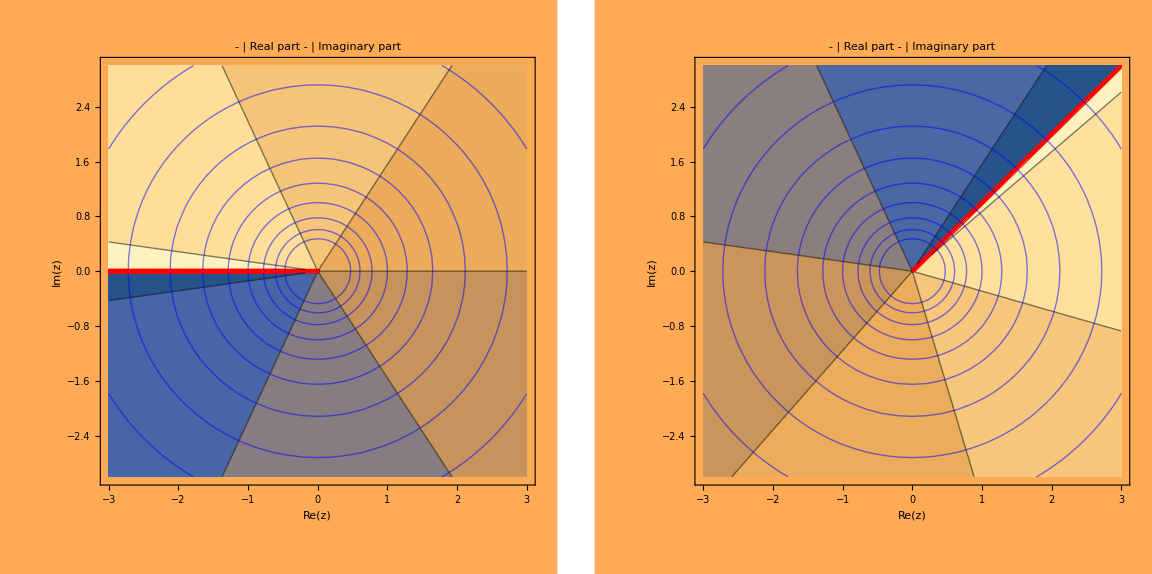

```mathematica
GraphicsRow[{plot[Log[z]],plot[log[z,π/4]]}]
```

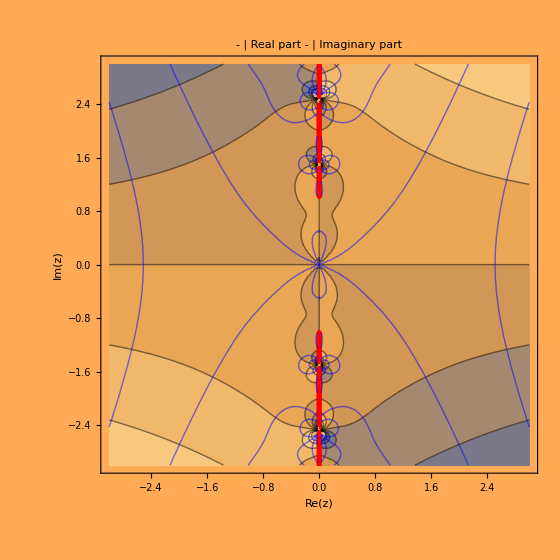

```mathematica
plot[z Tanh[π z] Log[z^2+1]]
```

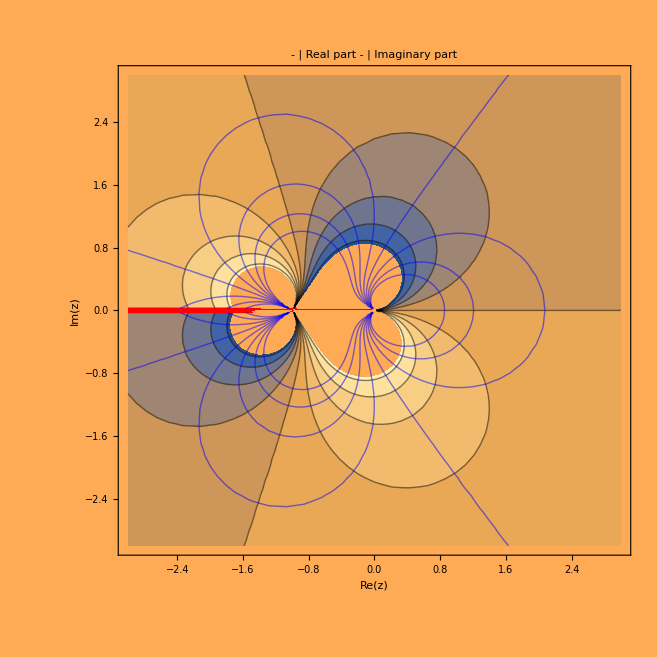

```mathematica
plot[z^(.33-1)/(z+1)]
```

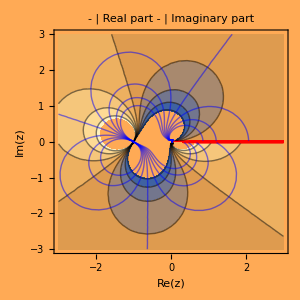

```mathematica
plot[E^((.33-1)log[z,0])/(z+1)]
```

```mathematica
Solve[4z^2+4z+3==0,z]
```

{{z→1/2 (-1-ⅈ √2)},{z→1/2 (-1+ⅈ √2)}}

```mathematica
Limit[1/Sqrt[4 z^2+4 z+2],z->ComplexInfinity]
```

0

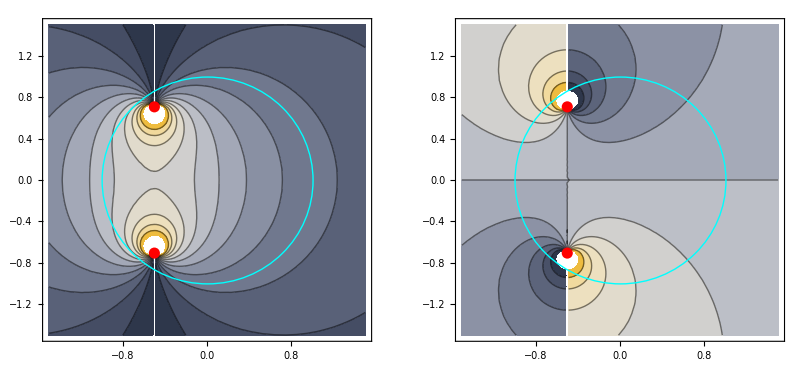

```mathematica
With[{z1=1/2 (-1-I Sqrt[2]),z2=1/2 (-1+I Sqrt[2])},GraphicsRow[Table[ContourPlot[g[1/Sqrt[4 (x+I y-z1) (x+I y-z2)]],{x,-1.5,1.5},{y,-1.5,1.5},ColorFunction->"GrayYellowTones",Epilog->{Cyan,Thick,Circle[{0,0}],Red,PointSize[0.02],Point[{Re@#,Im@#}&/@{z1,z2}]},Contours->11],{g,{Re,Im}}]]]
```

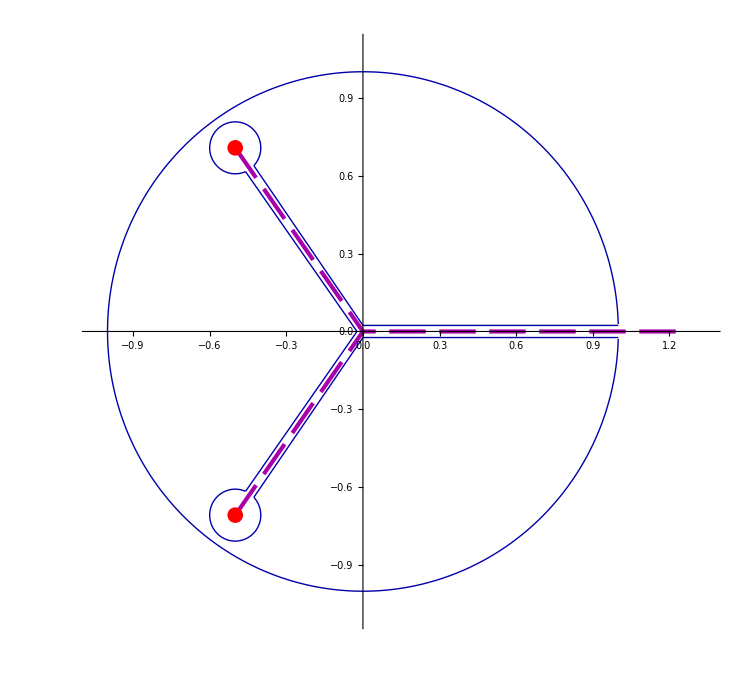

```mathematica
cp[{x_,y_},r_,t_,ϕ_,δ_]:=ConditionalExpression[{x,y}+r {Cos[t+ϕ],Sin[t+ϕ]},δ≤t≤2 Pi-δ]
Module[{z1=1/2 (-1-I Sqrt[2]),z2=1/2 (-1+I Sqrt[2]),z11,z22,r=1/10,δ,δ1},{z11,z22}={Re@#,Im@#}&/@{z1,z2};δ=2 r;δ1=δ/7;
ParametricPlot[{cp[{0,0},1,t,{0},δ1],cp[z11,r,t,-Pi+Arg[z1],δ],cp[z22,r,t,-Pi+Arg[z2],δ]},{t,0,2 Pi},PlotStyle->ConstantArray[{Thick,Darker@Blue},3],AxesStyle->Arrowheads[0.03],PlotRange->{{-1.05,1.35},{-1.1,1.1}},Epilog->{Darker@Blue,Thick,Line@{{cp[z11,r,δ,-Pi+Arg[z1],0],{Sin[Arg[z1]] δ1,0},cp[z22,r,2 Pi-δ,-Pi+Arg[z2],0]},{cp[z11,r,2 Pi-δ,-Pi+Arg[z1],0],{0,Sin[Arg[z1]] δ1},{1,Sin[Arg[z1]] δ1}},{cp[z22,r,δ,-Pi+Arg[z2],0],{0,-Sin[Arg[z1]] δ1},{1,-Sin[Arg[z1]] δ1}}},Darker@Magenta,Dashing[{0.035,0.013}],Thickness[0.004],Line@{{z11,{0,0},{1.25,0}},{z22,{0,0}}},Red,PointSize[0.015],Point[{z11,z22}]},ImageSize->750]]
```

```mathematica
With[{z1=1/2 (-1-I Sqrt[2]),z2=1/2 (-1+I Sqrt[2])},Limit[{Integrate[(r I E^(I t))/(2 Sqrt[r E^(I t) (r E^(I t)+z1-z2)]),{t,0,2 Pi},Assumptions->r>0],Integrate[(r I E^(I t))/(2 Sqrt[r E^(I t) (r E^(I t)+z2-z1)]),{t,0,2 Pi},Assumptions->r>0]},r->0]]
```

Limit::ztest: Unable to decide whether numeric quantities {-Log[((1+ⅈ) ((1-ⅈ)+√2))/(√2 ((1+ⅈ)+√2))],ⅈ Log[((1+ⅈ) ((1-ⅈ)+√2))/(√2 ((1+ⅈ)+√2))],Log[((1+ⅈ) ((1-ⅈ)+√2))/(√2 ((1+ⅈ)+√2))]} are equal to zero. Assuming they are.

{0,0}

```mathematica
FullSimplify[Plus@@With[{z1=1/2 (-1-I Sqrt[2]),z2=1/2 (-1+I Sqrt[2])},{2 Integrate[z2/Sqrt[4 (t-1) z2 (t z2-z1)],{t,0,1}],-2 Integrate[z1/Sqrt[4 (t-1) z1 (t z1-z2)],{t,0,1}]}]]
```

-2 ArcSinh[Root-0.237-0.746 ⅈRoot[3+8 #1^2+8 #1^4&,1]-0.2370363217903477]+2 ArcSinh[Root-0.237+0.746 ⅈRoot[3+8 #1^2+8 #1^4&,2]-0.2370363217903477]

```mathematica
lin[x_]:={Arrowheads[{{0.05,0.5}}],Arrow[Most@x]};
arc[x_]:={Arrowheads[{{0.05,0.5}}],Arrow[Table[x[[1]] {Cos[j],x[[-2]] Sin[j]},{j,x[[2]],x[[3]],0.01 (x[[3]]-x[[2]])}]]};
cont[lst_]:=If[#[[-1]]=="line",lin@#,arc@#]&/@lst
im[d_,o_]:=Graphics[{Red,cont[{{{o,d},{1,d},"line"},{1,ArcTan[d],2 Pi-ArcTan[d],1,"arc"},{{1,-d},{o,-d},"line"},{Norm[{o,d}],ArcTan[d/o],2 Pi-ArcTan[d/o],-1,"arc"}}],Black,Text["|z|=1/R",2 Norm[{o,d}] {Cos[3 Pi/4],Sin[3 Pi/4]}]},Axes->True,Ticks->{{{1.1,"R"},{-1.1,"-R"}},{{1.1,"i R"},{-1.1,"-i R"}}},PlotRange->{{-1.3,1.3},{-1.3,1.3}}]
```

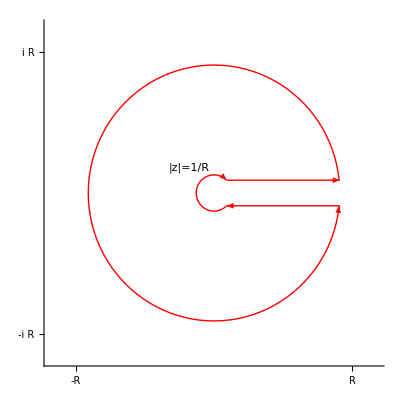

```mathematica
im[0.1,0.1]
```

```mathematica
With[{z=1/2+I t},Integrate[z^(-q-1) (1-z)^(-λ-1),{t,-Infinity,Infinity},Assumptions->{q≥0,λ>0}]]
```

(2 π Gamma[1+q+λ])/(Gamma[1+q] Gamma[1+λ])